```mathematica
ClearAll[files, importfile, raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/cq/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/cq/~$Книга1.xlsx}

```mathematica
importfile = files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр (Электричество и магнетизм)/cq/Книга1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

```mathematica
dataset1=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"a"->(Around[#a, #b] &),"c"-> (Around[#c, #d] &)|>]
```

Dataset[<>]

```mathematica
line1 =LinearModelFit[(Normal@dataset1[All,{"a","c"}/*Values]),{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+3.19407 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 3.19407 | 0.0228866 | 139.561 | 3.58302×10^-10

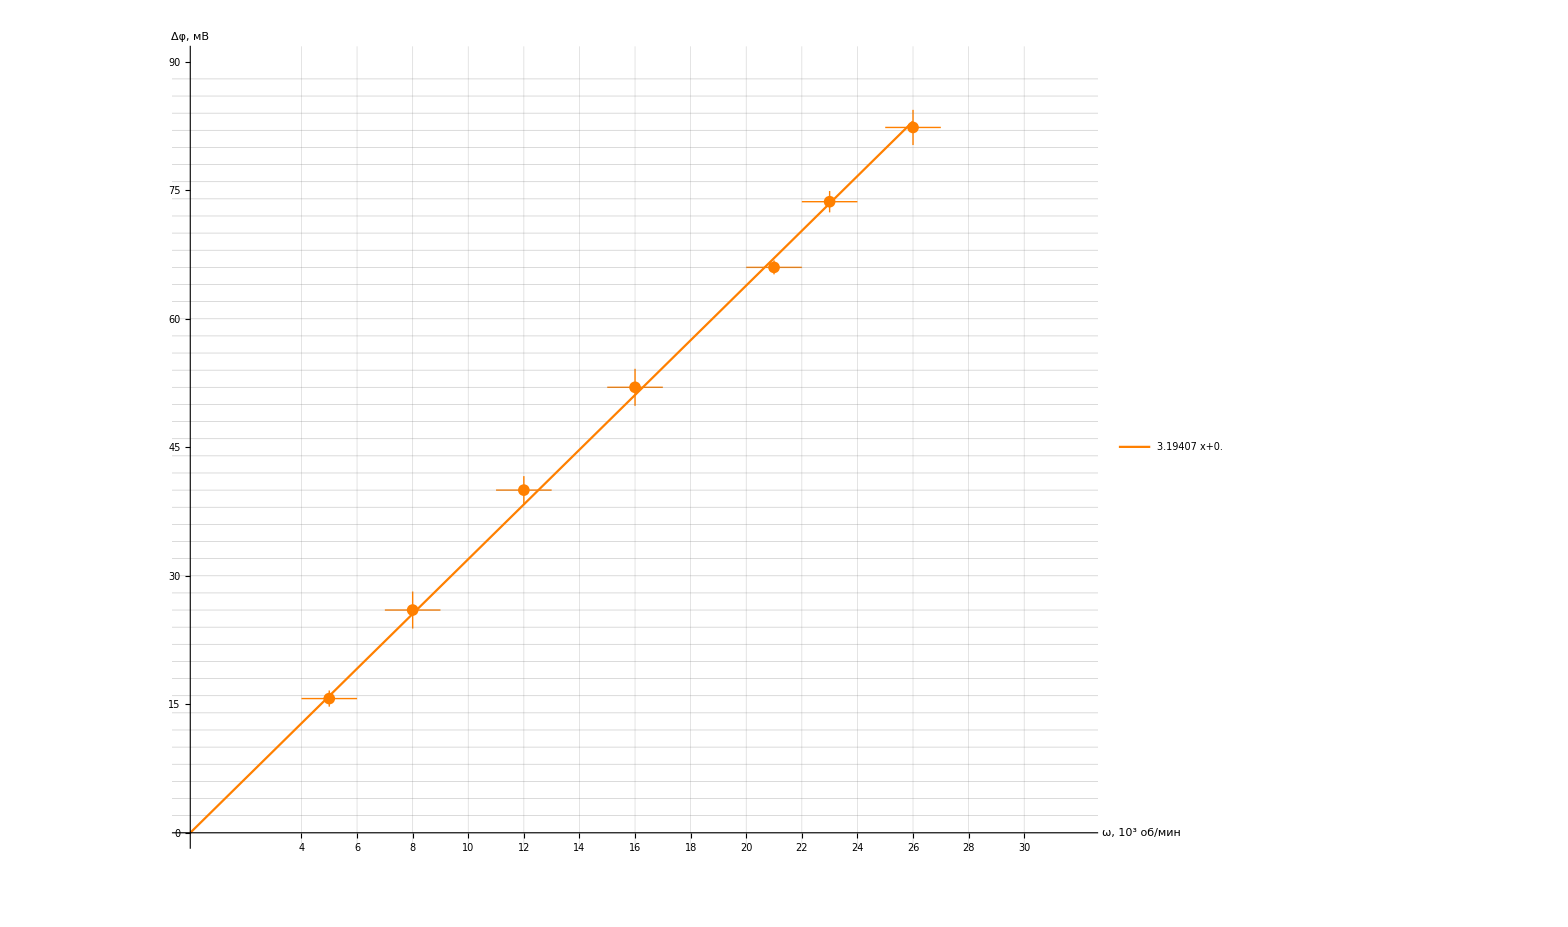

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
Ticks-> {Range[4,30,2],Range[0,1300,5]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["ω, 10^3 об/мин",Large],Style["Δφ, мB",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{0,32},{0,90}},

GridLines->{Range[-0.1,100,0.5], Range[-10,100,2]},
LabelStyle->Black,
PlotStyle->Orange
],
Plot[
{line1@x},
{x,0, 26},
PlotLegends->Placed[
LineLegend[
{Normal@line1, line1["ParameterTable"]},
LabelStyle->20
],
{Scaled[0.5],Scaled[0.75]}
],
PlotStyle->Orange
]
]
```